## Cloud Functions

### Working with Cloud Objects

#### Storing code on the cloud

We can create an object

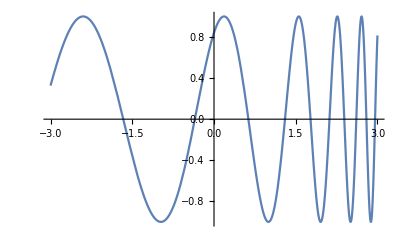

```mathematica
myFunctionPlot = Plot[Sin[2x +Exp[x]],{x,-3,3}]
```

And use CloudPut to store the information on the cloud

```mathematica
CloudPut[myFunctionPlot,"MyCloudStoredPlotCode"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/MyCloudStoredPlotCode]

This stores a pure expression in the cloud. We can get it back  by using the CloudGet function

```mathematica
CloudGet[CloudObject[["https://www.wolframcloud.com/obj/santiagoc/MyCloudStoredPlotCode"](https://www.wolframcloud.com/obj/santiagoc/MyCloudStoredPlotCode)]]
```

-Graphics-

Note that by going directly into the CloudObject URL you will get the raw code and not the pretty picture

```mathematica
SystemOpen["https://www.wolframcloud.com/obj/santiagoc/MyCloudStoredPlotCode"]
```

### Deploying objects

If we want something that actually runs in the cloud we would use CloudDeploy

```mathematica
CloudDeploy[myFunctionPlot,"myDeployedPlot"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myDeployedPlot]

You can CloudDeploy practically any Wolfram Language Expression

```mathematica
CloudDeploy[Manipulate[Plot[Sin[f x],{x,-Pi,Pi}],{f,1,10}],"myDeployedManipulate"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myDeployedManipulate]

```mathematica
SystemOpen[CloudObject[["https://www.wolframcloud.com/obj/santiagoc/myDeployedManipulate"](https://www.wolframcloud.com/obj/santiagoc/myDeployedManipulate)]]
```

Notice that the deployed object updates discretely (that is only after I “unclick” my mouse). We can make it flow more via setting the ContinuousAction option on the manipulate to True (Mind Zoom Bandwith)

```mathematica
CloudDeploy[Manipulate[Plot[Sin[f x],{x,-Pi,Pi}],{f,1,10},ContinuousAction->True],"myDeployedManipulate"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myDeployedManipulate]

#### Permissions

If we shared the link above we would run into the issue of people not signed into your account not being able to access it, as by default the permissions are set to private. There are a few ways in which these can be overcome

The first way is to change the permissions directly from the CloudDeploy

```mathematica
CloudDeploy[Manipulate[Plot[Sin[f x],{x,-Pi,Pi}],{f,1,10}],"myDeployedManipulate",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myDeployedManipulate]

Permissions can be set in many different ways. The above lets anyone go to your file.

Alternatively, you can Set specific permissions for different people

```mathematica
CloudDeploy[myFunctionPlot,"myDeployedPlot",Permissions->{"dstevens@wolfram.com"->{"Read","Write"}}]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myDeployedPlot]

If you want to avoid (for any reason) using permissions you can always just use the CloudPublish function

```mathematica
CloudPublish[Manipulate[Plot[Sin[f x],{x,-Pi,Pi}],{f,1,10}],"myDeployedManipulate"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myDeployedManipulate]

#### Question?

What is the function that can be used to store code in the cloud for later local retrieval?

### Databins

We can create a databin with the CreateDatabin function

```mathematica
CreateDatabin[]
```

Databin[…]

Once this is done you will get an email with some information

One thing we are really interested in recording is the ShortID. Which we can use to do computations with it.

```mathematica
bin=Databin["U3nir5QP"];
```

The first basic thing we can do is add information, you can in principle add any type of expression, but DaTaDrop works really well with associations.

```mathematica
DatabinAdd[bin,<|"FirstName"->"Santiago","LastName"->"Camacho","Age"->31|>]
```

Databin[…]

Note that it dynamically updates the originally created interface above. Let us add a few more values

```mathematica
DatabinAdd[bin,<|"FirstName"->"David","LastName"->"Stevens","Age"->26|>];
```

```mathematica
DatabinAdd[bin,<|"FirstName"->"Kelvin","LastName"->"Mischo","Age"->36|>];
```

To get the Information in the databin we can use the Values

```mathematica
bin["Values"]
```

<|FirstName→{Santiago,David,Kelvin},LastName→{Camacho,Stevens,Mischo},Age→{31,26,36}|>

We see that it saves everything as an association. Great for Dataset

```mathematica
dataset=Dataset[bin]
```

With this we can do any type of analytics on the information

```mathematica
dataset[Mean,"Age"]
```

31

```mathematica
dataset[Max,"Age"]
```

36

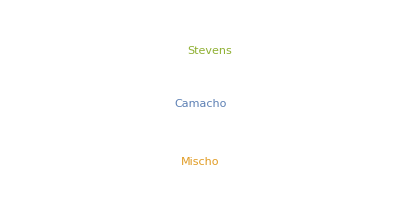

```mathematica
dataset[WordCloud,"LastName"]
```

### Forms

There are two main functions we will be interested in FormFunction and FormPage. Their final effect is a bit different but their outline is the same.

```mathematica
FormFunction[formspec,func]
```

```mathematica
FormFunction["number"->Integer,#number^2&]
```

FormFunction[]

```mathematica
FormPage["number"->Integer,#number^2&]
```

This is of course more interesting once you deploy these forms

```mathematica
CloudDeploy[FormPage["number"->Integer,#number^2&],"mySquareForm",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/mySquareForm]

```mathematica
SystemOpen[%]
```

You can use these together with created databins to store data on them

```mathematica
CloudDeploy[FormPage[{"first"->String,"last"->String,"age"->Integer},(DatabinAdd[Databin["U3nir5QP"],<|"FirstName"->#first,"LastName"->#last,"Age"->#age|>];
"Thank you for your submission")&],
"myNameForm",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myNameForm]

```mathematica
SystemOpen[%]
```

```mathematica
Dataset[bin]
```

We can further customize the look of the forms by changing the formspec values to be associations.

```mathematica
FormPage[{
"first"-><|"Interpreter"-> String,"Label"->"First Name"|>,
"last"-><|"Interpreter"-> String,"Label"->"Last Name","Hint"->"Smith"|>,
"age"-><|"Interpreter"->Integer,"Label"->"Age","Hint"->"22","Help"->"This is the number of years passed since you were born"|>
},(DatabinAdd[Databin["U3nir5QP"],<|"FirstName"->#first,"LastName"->#last,"Age"->#age|>];
"Thank you for your submission")&]
```

We can also add AppearanceRules and a PageTheme to it.

```mathematica
FormPage[{
"first"-><|"Interpreter"-> String,"Label"->"First Name"|>,
"last"-><|"Interpreter"-> String,"Label"->"Last Name","Hint"->"Smith"|>,
"age"-><|"Interpreter"->Integer,"Label"->"Age","Hint"->"22","Help"->"This is the number of years passed since you were born"|>
},(DatabinAdd[Databin["U3nir5QP"],<|"FirstName"->#first,"LastName"->#last,"Age"->#age|>];
"Thank you for your submission")&,
AppearanceRules-><|"Title"->Style["Identification Form",Blue,34],"Description"->"Please tell us a bit about yourself."|>,
PageTheme->"Black"]
```

```mathematica
CloudDeploy[%,"myNameForm",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/myNameForm]

### API creation and Deployment

The API outline is very similar to that of forms the main difference is that we use the APIFunction symbol to create them.

```mathematica
api=APIFunction["number"->Integer,#number^2&];
```

```mathematica
CloudDeploy[api,"MySquareAPI",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/santiagoc/MySquareAPI]

This really becomes useful when you are calling the API in an external program/webpage/language. And different environments  would execute the API in different ways (that is out of the scope of a Wolfram Language workshop) but for example to call an API using Wolfram Language we could use the URLExecute function

```mathematica
URLExecute["https://www.wolframcloud.com/obj/santiagoc/MySquareAPI",{"number"->12}]
```

144